Naloga 1

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

1.Podnaloga

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

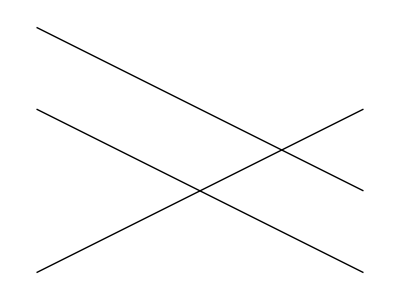

```mathematica
Narisi[d, d2, d3]
```

2. podnaloga

```mathematica
ClearAll[x, y]

EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

Naloga 2

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

Naloga 3

```mathematica
m1 = Mnogokotnik[{0,0},{1,1}, {0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

1. podnaloga

```mathematica
Slika[Mnogokotnik[t__]] :=Line[{t}]
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

2. Podnaloga

```mathematica
m1 = Append[m1, First[m1]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

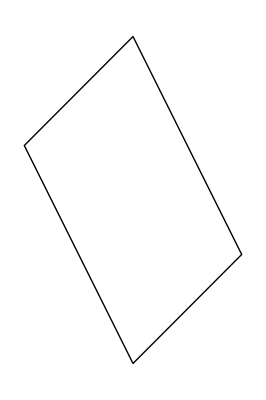

```mathematica
Narisi[m__Mnogokotnik]:= Graphics[Map[Slika, List[m]]]
Narisi[m1]
```

3. podnaloga

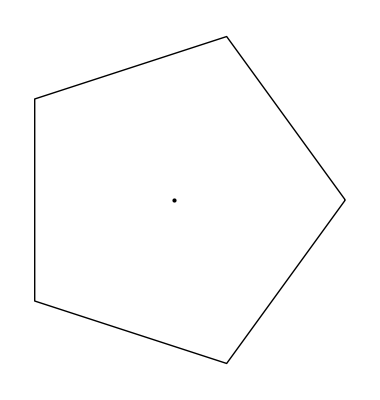

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]

p5= PravilniNKotnik[5,2]
```

4. podnaloga

```mathematica
PravilniNKotnik[n_, r_, phi_]:= Manipulate[Graphics[
{Line[Table[{r*Cos[(2Pi*i + x)/n],r*Sin[(2Pi*i + x)/n]},{i,0,n}]],Point[{0,0}]}], {x, 0, Pi}]

PravilniNKotnik[5,2,Pi]
```

5. podnaloga

```mathematica
Daljice[Mnogokotnik[t__]] := Partition[{t}, {2,2},1]
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Daljice[m1]
```

{{{{0,0},{1,1}}},{{{1,1},{0,3}}},{{{0,3},{-1,2}}},{{{-1,2},{0,0}}}}

```mathematica
4. naloga
```

```mathematica
d = Daljica[{-1,1},{3,-1}];
d2 = Daljica[{-1,-1}, {3,1}];
d3 = Daljcia[{-1,2},{3,0}];
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Presek[m_Mnogokotnik[AA_, BB_], d_Daljica[CC_,DD_]]:= Module[{a, b},
a = Daljice[m1];
b = d;
resitev = Solve[{AA + r * (BB - AA)== CC + s * (DD - CC), s ≥ 0, s≤ 1, r ≥ 0, r≤ 1}, {x, y}]]
Presek[m1, d]
```

Presek[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],Daljica[{-1,1},{3,-1}]]

```mathematica
Presek[m1,m2]
```

Presek[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],m2]

5. naloga

```mathematica
VsiPari[f_, sez1_, sez2_]:= Flatten[Outer[f, sez1, sez2], 1]
VsiPari[f, {1, 2,3 },{a, b}]
{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}
```

1. podnaloga

```mathematica
Outer[f, {1,2,3},{a,b}]
{{f[1,a],f[1,b]},{f[2,a],f[2,b]},{f[3,a],f[3,b]}}

Outer[{c,3},{4,3,{6}},{g,{f,h}},2]
{{{c,3}[4,g],{{c,3}[4,f],{c,3}[4,h]}},{{c,3}[3,g],{{c,3}[3,f],{c,3}[3,h]}},{{{c,3}[6,g],{{c,3}[6,f],{c,3}[6,h]}}}}
```

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 1]
{b,2,1,3,{4},f,{g,h}}

Flatten[[f, {1,2,3},{a,b}]]
Part::pkspec1: "The expression \!\(\*RowBox[{\"f\"}]\) cannot be used as a part specification."
Flatten⟦f,{1,2,3},{a,b}⟧
```

2. podnaloga

```mathematica
m2 = Mnogokotnik[{0,0},{0,-1},{1,2},{-1, 2}]
m3 = Mnogokotnik[{0,1},{1,4},{2,3},{-5, 2}]
```

```mathematica
Mnogokotnik[{0,0},{0,-1},{1,2},{-1,2}]. i
```

Mnogokotnik[{0,1},{1,4},{2,3},{-5,2}]

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:= VsiPari[f, m1, m2]
Presek[m1,m2]
```

VsiPari[f,Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],Mnogokotnik[{0,0},{0,-1},{1,2},{-1,2}]]

```mathematica
Presek[m1,m3]
```

VsiPari[f,Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],Mnogokotnik[{0,1},{1,4},{2,3},{-5,2}]]

6. Naloga

### Imamo △ s točkami A(2,4), B(1,5), C(3,2). Izračunaj enotske vektorje AB, BC, CA, ter nariši ta △!

```mathematica
AA = {2,4}
```

{2,4}

```mathematica
BB = {1,5}
```

{1,5}

```mathematica
CC = {2,3}
```

{2,3}

```mathematica
Vektor[A_,B_]:=Norm[A-B]
```

```mathematica
EnotskiVektor[A_,B_]:=(B-A)/Vektor[A,B]
```

```mathematica
EnotskiVektor[AA,BB]
```

{-1/(√2),1/(√2)}

```mathematica
EnotskiVektor[BB,CC]
```

{1/(√5),-2/(√5)}

```mathematica
EnotskiVektor[CC,AA]
```

{0,1}

```mathematica
Trikotnik = {AA,BB,CC}
```

{{2,4},{1,5},{2,3}}

```mathematica
Tocke = Append[Trikotnik, Trikotnik[[1]]]
```

{{2,4},{1,5},{2,3},{2,4}}

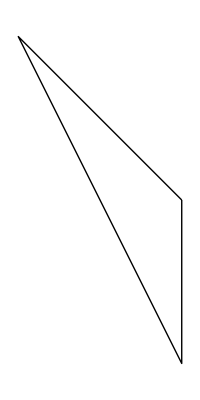

```mathematica
NarisiTrikotnik[tocke_] := Graphics[Line[Tocke]]
NarisiTrikotnik[Tocke]
```